## Preamble

```mathematica
$Assumptions={w12>0,w13>0,w14>0,w15>0,w27>0,w31>0,w32>0,w41>0,w52>0,w63>0,w64>0,w65>0,w74>0,w75>0,w76>0,t1>0,t2>0,t3>0,t4>0,t5>0,t6>0,t7>0};
w14max=(-1-w12 w27 w41 w74+w27 w52 w74+w12 w27 w31 w63 w76-w27 w32 w63 w76-w12 w27 w41 w64 w76+w27 w52 w64 w76-w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w74+w64 w76)))/(-w41-w27 w32 w41 w63 w76+w27 w31 w52 w63 w76);
g1=Simplify[(t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41)))-t1 t2 t3 t4 t5 t6 t7 (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))];
g2=Simplify[-t1 t2 t3 t4 t5 t6 t7 (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))^2+(t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) ((t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))+t1 t2 t3 t4 t5 t6 t7 (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))-(t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76)))))];
g3=((t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) ((t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41)))-t1 t2 t3 t4 t5 t6 t7 (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))) (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))+t1^2 t2^2 t3^2 t4^2 t5^2 t6^2 t7^2 (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))^2+(t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))))^2 (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76))))^2-((t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41)))-t1 t2 t3 t4 t5 t6 t7 (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))) ((t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76)))-t1 t2 t3 t4 t5 t6 t7 (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))))+(t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76)))) ((t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (-t3 t4 t5 t6-t3 t4 t5 t7-t3 t4 t6 t7-t3 t5 t6 t7-t4 t5 t6 t7-t4 t5 t6 t7 w13 w31+t3 t5 t6 t7 w14 w41-t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))-t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))+t1 t2 t3 t4 t5 t6 t7 (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))^2-2 t1 t2 t3 t4 t5 t6 t7 (t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76))))) ((t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (-t3 t4 t5 t6-t3 t4 t5 t7-t3 t4 t6 t7-t3 t5 t6 t7-t4 t5 t6 t7-t4 t5 t6 t7 w13 w31+t3 t5 t6 t7 w14 w41-t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))-t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))+t1 t2 t3 t4 t5 t6 t7 (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))^2+(t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (-t1 t2 t3 t4 t5 t6 t7 (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))+(t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76))))));
g14=t1^2 t2^2 t3^2 t4^2 t5^2 t6^2 t7^2 ((t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76)))^2-2 (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))) (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))+(t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))^3)+t1 t2 t3 t4 t5 t6 t7 (-2 (t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))))^2 (t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76)))+(t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76))) (3 (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76)))+(t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76)))-2 (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76)))))+(t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (-(t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))^2+(t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76))))+(t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) ((t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (-t3-t4-t5-t6-t7-t4 w13 w31-t5 w13 w31-t6 w13 w31-t7 w13 w31+t3 w14 w41+t5 w14 w41+t6 w14 w41+t7 w14 w41+t2 (-1-w13 w31+w14 w41)-t3 w12 w27 w41 w74-t5 w12 w27 w41 w74-t6 w12 w27 w41 w74-t5 w13 w27 w32 w41 w74-t6 w13 w27 w32 w41 w74+t3 w15 w27 w41 w52 w74+t6 w15 w27 w41 w52 w74+t3 w27 w52 w75+t4 w27 w52 w75+t6 w27 w52 w75+t4 w13 w27 w31 w52 w75+t6 w13 w27 w31 w52 w75-t3 w14 w27 w41 w52 w75-t6 w14 w27 w41 w52 w75+t4 w12 w27 w31 w63 w76+t5 w12 w27 w31 w63 w76-t4 w27 w32 w63 w76-t5 w27 w32 w63 w76+t5 w14 w27 w32 w41 w63 w76-t4 w15 w27 w31 w52 w63 w76-t3 w12 w27 w41 w64 w76-t5 w12 w27 w41 w64 w76-t5 w13 w27 w32 w41 w64 w76+t3 w15 w27 w41 w52 w64 w76+t3 w27 w52 w65 w76+t4 w27 w52 w65 w76+t4 w13 w27 w31 w52 w65 w76-t3 w14 w27 w41 w52 w65 w76+t1 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76)))+(t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))))))+(t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) ((t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))))^2 (t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76)))^2+(t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) ((t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))^2+(t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (-t3 t4-t3 t5-t4 t5-t3 t6-t4 t6-t5 t6-t3 t7-t4 t7-t5 t7-t6 t7-t4 t5 w13 w31-t4 t6 w13 w31-t5 t6 w13 w31-t4 t7 w13 w31-t5 t7 w13 w31-t6 t7 w13 w31+t3 t5 w14 w41+t3 t6 w14 w41+t5 t6 w14 w41+t3 t7 w14 w41+t5 t7 w14 w41+t6 t7 w14 w41-t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))-t3 t5 w12 w27 w41 w74-t3 t6 w12 w27 w41 w74-t5 t6 w12 w27 w41 w74-t5 t6 w13 w27 w32 w41 w74+t3 t6 w15 w27 w41 w52 w74+t3 t4 w27 w52 w75+t3 t6 w27 w52 w75+t4 t6 w27 w52 w75+t4 t6 w13 w27 w31 w52 w75-t3 t6 w14 w27 w41 w52 w75+t4 t5 w12 w27 w31 w63 w76-t4 t5 w27 w32 w63 w76-t3 t5 w12 w27 w41 w64 w76+t3 t4 w27 w52 w65 w76-t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76))))+(t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) ((t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76)))-(t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76)))))+(t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) ((t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76)))) ((t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (-t3-t4-t5-t6-t7-t4 w13 w31-t5 w13 w31-t6 w13 w31-t7 w13 w31+t3 w14 w41+t5 w14 w41+t6 w14 w41+t7 w14 w41+t2 (-1-w13 w31+w14 w41)-t3 w12 w27 w41 w74-t5 w12 w27 w41 w74-t6 w12 w27 w41 w74-t5 w13 w27 w32 w41 w74-t6 w13 w27 w32 w41 w74+t3 w15 w27 w41 w52 w74+t6 w15 w27 w41 w52 w74+t3 w27 w52 w75+t4 w27 w52 w75+t6 w27 w52 w75+t4 w13 w27 w31 w52 w75+t6 w13 w27 w31 w52 w75-t3 w14 w27 w41 w52 w75-t6 w14 w27 w41 w52 w75+t4 w12 w27 w31 w63 w76+t5 w12 w27 w31 w63 w76-t4 w27 w32 w63 w76-t5 w27 w32 w63 w76+t5 w14 w27 w32 w41 w63 w76-t4 w15 w27 w31 w52 w63 w76-t3 w12 w27 w41 w64 w76-t5 w12 w27 w41 w64 w76-t5 w13 w27 w32 w41 w64 w76+t3 w15 w27 w41 w52 w64 w76+t3 w27 w52 w65 w76+t4 w27 w52 w65 w76+t4 w13 w27 w31 w52 w65 w76-t3 w14 w27 w41 w52 w65 w76+t1 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76)))+(t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))))+(t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76))) (-2 (t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76)))+(t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76))))^2)));
g15=t1^2 t2^2 t3^2 t4^2 t5^2 t6^2 t7^2 ((t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76))) (3 (t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76)))^2-3 (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))) (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))+(t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))^3)+(1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))) ((t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))) (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))+2 (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76))))-(t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))^2 (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76))))))-t1 t2 t3 t4 t5 t6 t7 ((t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76)))^2 ((t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))^3+3 (t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))))^2 (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76)))-3 (t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76))))+(1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))) ((1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))) ((t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41)))^2 (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))+t1^2 t2^2 t3^2 t4^2 t5^2 t6^2 t7^2 (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))))+(t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76)))) (3 (t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76)))+(t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (-t3 t4-t3 t5-t4 t5-t3 t6-t4 t6-t5 t6-t3 t7-t4 t7-t5 t7-t6 t7-t4 t5 w13 w31-t4 t6 w13 w31-t5 t6 w13 w31-t4 t7 w13 w31-t5 t7 w13 w31-t6 t7 w13 w31+t3 t5 w14 w41+t3 t6 w14 w41+t5 t6 w14 w41+t3 t7 w14 w41+t5 t7 w14 w41+t6 t7 w14 w41-t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))-t3 t5 w12 w27 w41 w74-t3 t6 w12 w27 w41 w74-t5 t6 w12 w27 w41 w74-t5 t6 w13 w27 w32 w41 w74+t3 t6 w15 w27 w41 w52 w74+t3 t4 w27 w52 w75+t3 t6 w27 w52 w75+t4 t6 w27 w52 w75+t4 t6 w13 w27 w31 w52 w75-t3 t6 w14 w27 w41 w52 w75+t4 t5 w12 w27 w31 w63 w76-t4 t5 w27 w32 w63 w76-t3 t5 w12 w27 w41 w64 w76+t3 t4 w27 w52 w65 w76-t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76))))+(t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76))))^2 ((t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))^2-2 (t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))))+(t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76))) ((t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))) (-2 (t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))+(t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76)))))+(t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))^2 ((t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))+2 (t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76)))))-(t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76))) ((t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) (t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76)))+(t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))^2 (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76)))))))+(t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) ((t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))))^2 (t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76)))^3-(t2 t3 t4 t5 t6 t7+t1 (t2 t4 t5 t6 t7+t3 t4 t5 t6 t7+t2 t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7)))) ((1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76))))^3+(t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76)))^2 (2 (t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))+(t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76)))))-(t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76)))) (3 (t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76)))+(t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76))))))+(t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) ((t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75))))^2 (t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76)))^2+(1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76))) ((t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41)))^2 (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76)))-(t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76))))+(t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76))))^2)+(t1+t2+t3+t4+t5+t6+t7+t2 w13 w31+t4 w13 w31+t5 w13 w31+t6 w13 w31+t7 w13 w31-t2 w14 w41-t3 w14 w41-t5 w14 w41-t6 w14 w41-t7 w14 w41+t3 w12 w27 w41 w74+t5 w12 w27 w41 w74+t6 w12 w27 w41 w74+t5 w13 w27 w32 w41 w74+t6 w13 w27 w32 w41 w74-t3 w15 w27 w41 w52 w74-t6 w15 w27 w41 w52 w74-t3 w27 w52 w75-t4 w27 w52 w75-t6 w27 w52 w75-t4 w13 w27 w31 w52 w75-t6 w13 w27 w31 w52 w75+t3 w14 w27 w41 w52 w75+t6 w14 w27 w41 w52 w75-t4 w12 w27 w31 w63 w76-t5 w12 w27 w31 w63 w76+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t5 w14 w27 w32 w41 w63 w76+t4 w15 w27 w31 w52 w63 w76+t3 w12 w27 w41 w64 w76+t5 w12 w27 w41 w64 w76+t5 w13 w27 w32 w41 w64 w76-t3 w15 w27 w41 w52 w64 w76-t3 w27 w52 w65 w76-t4 w27 w52 w65 w76-t4 w13 w27 w31 w52 w65 w76+t3 w14 w27 w41 w52 w65 w76+t1 w27 (w32 w63 w76-w52 (w75+w65 w76))) ((t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (-t3 t4-t3 t5-t4 t5-t3 t6-t4 t6-t5 t6-t3 t7-t4 t7-t5 t7-t6 t7-t4 t5 w13 w31-t4 t6 w13 w31-t5 t6 w13 w31-t4 t7 w13 w31-t5 t7 w13 w31-t6 t7 w13 w31+t3 t5 w14 w41+t3 t6 w14 w41+t5 t6 w14 w41+t3 t7 w14 w41+t5 t7 w14 w41+t6 t7 w14 w41-t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))-t3 t5 w12 w27 w41 w74-t3 t6 w12 w27 w41 w74-t5 t6 w12 w27 w41 w74-t5 t6 w13 w27 w32 w41 w74+t3 t6 w15 w27 w41 w52 w74+t3 t4 w27 w52 w75+t3 t6 w27 w52 w75+t4 t6 w27 w52 w75+t4 t6 w13 w27 w31 w52 w75-t3 t6 w14 w27 w41 w52 w75+t4 t5 w12 w27 w31 w63 w76-t4 t5 w27 w32 w63 w76-t3 t5 w12 w27 w41 w64 w76+t3 t4 w27 w52 w65 w76-t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76))) (t3 t4 t5+t3 t4 t6+t3 t5 t6+t4 t5 t6+t3 t4 t7+t3 t5 t7+t4 t5 t7+t3 t6 t7+t4 t6 t7+t5 t6 t7+t4 t5 t6 w13 w31+t4 t5 t7 w13 w31+t4 t6 t7 w13 w31+t5 t6 t7 w13 w31-t3 t5 t6 w14 w41-t3 t5 t7 w14 w41-t3 t6 t7 w14 w41-t5 t6 t7 w14 w41+t2 (t4 (t5+t6+t7) (1+w13 w31)+(t6 t7+t5 (t6+t7)) (1+w13 w31-w14 w41)+t3 (t4-(t5+t6+t7) (-1+w14 w41)))+t3 t5 t6 w12 w27 w41 w74-t3 t4 t6 w27 w52 w75+t1 (t4 t5+t4 t6+t5 t6+t4 t7+t5 t7+t6 t7+t2 (t3+t4+t5+t6+t7)-t4 t6 w27 w52 w75+t4 t5 w27 w32 w63 w76+t3 (t4+t5+t6+t7-t6 w27 w52 w75-t4 w27 w52 (w75+w65 w76))))+(t3 t4 t5 t6 t7+t1 (t4 t5 t6 t7+t3 (t4 t6 t7+t5 t6 t7+t4 t5 (t6+t7))+t2 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7))))+t2 t4 t5 t6 t7 (1+w13 w31)+t2 t3 (t4 t6 t7+t4 t5 (t6+t7)+t5 t6 t7 (1-w14 w41))) (-2 (t3 t4 t5 t6+t3 t4 t5 t7+t3 t4 t6 t7+t3 t5 t6 t7+t4 t5 t6 t7+t4 t5 t6 t7 w13 w31-t3 t5 t6 t7 w14 w41+t2 (t4 (t6 t7+t5 (t6+t7)) (1+w13 w31)+t5 t6 t7 (1+w13 w31-w14 w41)+t3 (t4 (t5+t6+t7)-(t6 t7+t5 (t6+t7)) (-1+w14 w41)))+t1 (t4 t5 t6+t4 t5 t7+t4 t6 t7+t5 t6 t7+t2 (t5 t6+t5 t7+t6 t7+t4 (t5+t6+t7)+t3 (t4+t5+t6+t7))+t3 (t6 t7+t5 (t6+t7)+t4 (t5+t6+t7-t6 w27 w52 w75)))) (1+w12 w27 w41 w74-w15 w27 w41 w52 w74-w27 w52 w75-w12 w27 w31 w63 w76+w27 w32 w63 w76+w15 w27 w31 w52 w63 w76+w12 w27 w41 w64 w76-w15 w27 w41 w52 w64 w76-w27 w52 w65 w76+w14 w41 (-1-w27 w32 w63 w76+w27 w52 (w75+w65 w76))+w13 (w31+w27 w32 w41 (w74+w64 w76)-w27 w31 w52 (w75+w65 w76)))+(t3 t4+t3 t5+t4 t5+t3 t6+t4 t6+t5 t6+t3 t7+t4 t7+t5 t7+t6 t7+t4 t5 w13 w31+t4 t6 w13 w31+t5 t6 w13 w31+t4 t7 w13 w31+t5 t7 w13 w31+t6 t7 w13 w31-t3 t5 w14 w41-t3 t6 w14 w41-t5 t6 w14 w41-t3 t7 w14 w41-t5 t7 w14 w41-t6 t7 w14 w41+t2 (t3+t4+t4 w13 w31-t3 w14 w41+(t5+t6+t7) (1+w13 w31-w14 w41))+t3 t5 w12 w27 w41 w74+t3 t6 w12 w27 w41 w74+t5 t6 w12 w27 w41 w74+t5 t6 w13 w27 w32 w41 w74-t3 t6 w15 w27 w41 w52 w74-t3 t4 w27 w52 w75-t3 t6 w27 w52 w75-t4 t6 w27 w52 w75-t4 t6 w13 w27 w31 w52 w75+t3 t6 w14 w27 w41 w52 w75-t4 t5 w12 w27 w31 w63 w76+t4 t5 w27 w32 w63 w76+t3 t5 w12 w27 w41 w64 w76-t3 t4 w27 w52 w65 w76+t1 (t2+t4+t5+t6+t7-t4 w27 w52 w75-t6 w27 w52 w75+t4 w27 w32 w63 w76+t5 w27 w32 w63 w76-t4 w27 w52 w65 w76-t3 (-1+w27 w52 w75+w27 w52 w65 w76)))^2))));
```

{True,True,w14>0,True,True,True,True,True,True,True,True,w65>0,True,w75>0,True,True,True,True,True,True,True,True}

```mathematica
G1=Simplify[g1/.{w15->w14,w65->w64,w75->w74}];
G2=g2/.{w15->w14,w65->w64,w75->w74};
G3=g3/.{w15->w14,w65->w64,w75->w74};
G4=g14/.{w15->w14,w65->w64,w75->w74};
G5=g15/.{w15->w14,w65->w64,w75->w74};
```

## Random Weight Visualisation

Run the code below to visualize examples of the 5 stability conditions using random weights 0<w_ij<30.

w14 Plotted Range: 0 -> 116.989

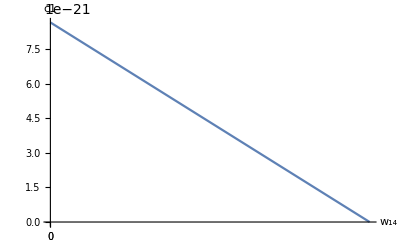
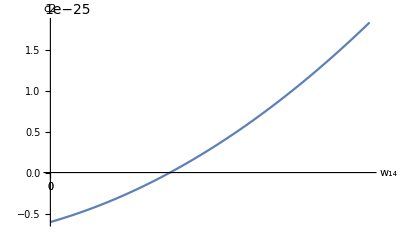
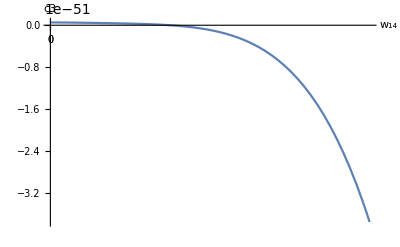
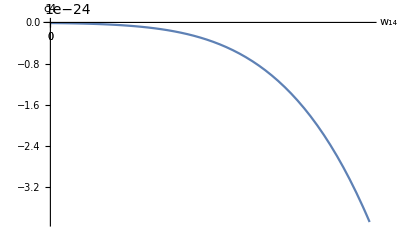
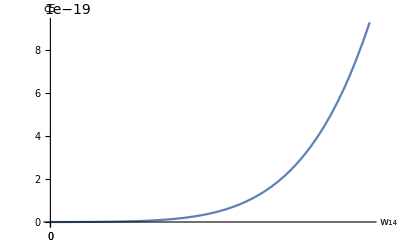

```mathematica
m=0;
M=30;
t1=.001*14;t2=.001*8;t3=.001*6;t4=.001*2.6;t5=.001*2.6;t6=.001*16.1;t7=.001*13.8;w12=RandomReal[{m,M}];w13=RandomReal[{m,M}];w15=RandomReal[{m,M}];w27=RandomReal[{m,M}];w31=RandomReal[{m,M}];w32=RandomReal[{m,M}];w41=RandomReal[{m,M}];w52=RandomReal[{m,M}];w63=RandomReal[{m,M}];w64=RandomReal[{m,M}];w74=RandomReal[{m,M}];w76=RandomReal[{m,M}];
s=Solve[G1==0,w14];
pM=w14/.s[[1]];
If[
w27 w31 w52 w63 w76>w41+w27 w32 w41 w63 w76,pM=Simplify[w14max],m=Max[0,w14max]];
p1=Plot[G1,{w14,m,pM},AxesLabel->{Subscript[w, 14],c1},Ticks->{0{None,Automatic},{None,Automatic}}];
p2=Plot[G2,{w14,m,pM},AxesLabel->{Subscript[w, 14],c2},Ticks->{0{None,Automatic},{None,Automatic}}];
p3=Plot[G3,{w14,m,pM},AxesLabel->{Subscript[w, 14],c3},Ticks->{0{None,Automatic},{None,Automatic}}];
p4=Plot[-G4,{w14,m,pM},AxesLabel->{Subscript[w, 14],c4},Ticks->{0{None,Automatic},{None,Automatic}}];
p5=Plot[-G5,{w14,m,pM},AxesLabel->{Subscript[w, 14],c5},Ticks->{0{None,Automatic},{None,Automatic}}];
Print["w14 Plotted Range: ", m," -> ", pM]
Row[{p1,p2,p3,p4,p5}]
```

The system is stable for values of w_14 in which all the graphs are above 0.